```mathematica
(*Define the variables*)
d = Symbol["d"];
r=Symbol["r"];
t=Symbol["t"];
s=Symbol["s"];
(*create some useful helper variables to simplify the algebra*)
tau = - Log[d]/r;
b=Exp[-r*(tau-t)*(1+s)];
g=(1-b)*(1-d);
(*calculate the probability of i mutants remaining after the bottleneck, defining i=0 separately*)
P[i_]=b(1-d)(d/(1-d))^i * Sum[g^(j-1)*Binomial[j,i],{j,i,Infinity}];
p0 = b (1-d) Sum[g^(j-1)*Binomial[j,0],{j,1,Infinity}];
(*Define phi as the nontrivial solution*)
solution = Solve[phi==p0+Sum[P[i]*phi^i,{i,1,Infinity}]/.t->0,phi];
phi=phi/. Select[solution,#=!={phi->1}&][[1]]
```

((-1+d) d^s)/(-1+d^(1+s))

```mathematica
(*Using phi, find the chance of extinction for any t and s, V(t,s)*)
v = p0+Sum[P[i]*phi^i,{i,1,Infinity}]
```

-((-1+d) d^(-1+s) ⅇ^(-r (1+s) (-t-Log[d]/r)))/((-1-d^s ⅇ^(r t+r s t)+d^(1+s) ⅇ^(r t+r s t)) (-1+d^s-d^s ⅇ^(r t+r s t)+d^(1+s) ⅇ^(r t+r s t)))-((-1+d) ⅇ^(-r (1+s) (-t-Log[d]/r)) (-1+ⅇ^(r (1+s) (-t-Log[d]/r))))/((1-ⅇ^(-r (1+s) (-t-Log[d]/r))) (1-d+d ⅇ^(r (1+s) (-t-Log[d]/r))))

```mathematica
(*find the rate of mutations ocfcuring that will eventually fix at time t and effect size s*)
integrand = Simplify[d r Exp[r t](1-v)/tau]
```

-(d (-1+d^s) ⅇ^(r t) r^2)/((-1+d^(1+s) ⅇ^(r (1+s) t)-d^s (-1+ⅇ^(r (1+s) t))) Log[d])

```mathematica
(*find the rate over all times t*)
integral=Integrate[integrand,{t,0,tau},Assumptions->{r>0,d>0,d<1,t>0,s>0}]
```

-1/Log[d]r (Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-(-1+d)/(d (-1+d^s))]-d Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-((-1+d) d^s)/(-1+d^s)])

```mathematica
(*there is no closed form integral available over values of s*)
Integrate[integral*a*Exp[-a*s],{s,0,Infinity}]
```

∫_0^∞ -1/Log[d]a ⅇ^(-a s) r (Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-(-1+d)/(d (-1+d^s))]-d Hypergeometric2F1[1,1/(1+s),1+1/(1+s),-((-1+d) d^s)/(-1+d^s)])ⅆs

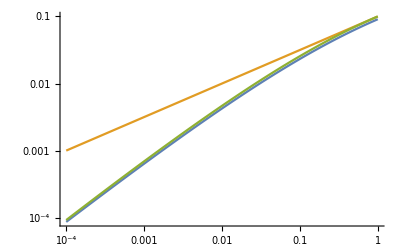

```mathematica
(*Check how good the approximations are*)
LogLogPlot[Evaluate[{integral,r s Sqrt[d],r s Log[1/d]/(1/d-1)} /. {r->1,s->0.1}],{d,0.0001,1}]
```

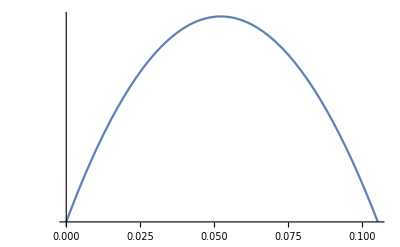

```mathematica
(*Check the rate at different times t*)
LogPlot[Evaluate[integrand/. {r->1,s->0.1,d->0.9001}],{t,0,tau/.{r->1,d->0.9001}}]
```